## Quantum-Zeno Based Molecule detection

```mathematica
init = P[-1] == {1,0}; (*Atom position in |L>, |R> basis*)
P[t_] = {pL[t],pR[t]};
J =1;
H[t_] = {{Δ, -J},{-J, -Δ - ⅈ γ/2 }};
SE = ⅈ P'[t] == H[t].P[t];

PSoln = ParametricNDSolve[{SE ,init},{pL,pR},{t,-1,3},{Δ,γ}];
```

```mathematica
Landau-Zener Transfer (no loss)
```

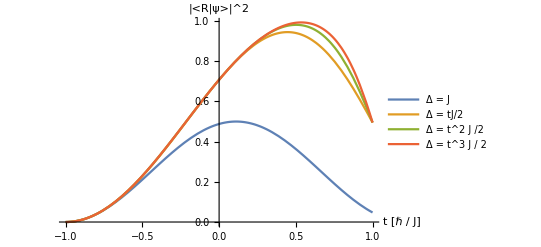

```mathematica
Plot[{Evaluate[Abs[pR[1,0][t]]^2/. PSoln ],Evaluate[Abs[pR[t/2,0][t]]^2/. PSoln],Evaluate[Abs[pR[t^2 / 2,0][t]]^2/. PSoln],Evaluate[Abs[pR[t^3 / 2,0][t]]^2/. PSoln]},{t,-1,1},PlotLegends->{"Δ = J","Δ = tJ/2", "Δ = t^2 J /2", "Δ = t^3 J / 2"}, AxesLabel->{"t [ℏ / J]","|<R|ψ>|^2"}, PlotRange->All]
```

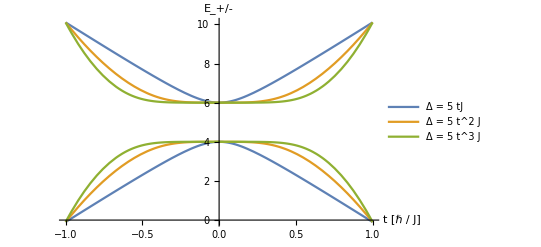

```mathematica
Plot[{Eigenvalues[H[t]] /. {Δ-> 5 t,  γ-> 0}, Eigenvalues[H[t]] /. {Δ-> 5t^2,  γ-> 0} , Eigenvalues[H[t]] /. {Δ-> 5t^3,  γ-> 0}},{t,-1,1},PlotLegends->{"Δ = 5 tJ", "Δ = 5 t^2 J", "Δ = 5 t^3 J "}, AxesLabel->{"t [ℏ / J]", "E_+/-"}]
```

```mathematica
Eigenvalues[H[t],2]
```

{1/4 (-ⅈ γ-√(16-γ^2+8 ⅈ γ Δ+16 Δ^2)),1/4 (-ⅈ γ+√(16-γ^2+8 ⅈ γ Δ+16 Δ^2))}

### Transfer with and without loss

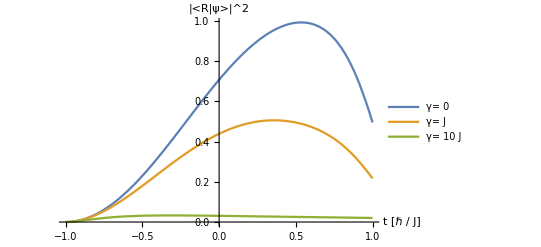

```mathematica
Plot[{ Evaluate[Abs[pR[t^3 / 2,0][t]]^2/. PSoln], Evaluate[Abs[pR[t^3 / 2,1][t]]^2/. PSoln], Evaluate[Abs[pR[t^3 / 2,10][t]]^2/. PSoln]},{t,-1,1},PlotLegends->{"γ= 0", "γ= J", "γ= 10 J"}, AxesLabel->{"t [ℏ / J]","|<R|ψ>|^2"}]
```

See almost complete blockade of transfer with loss!

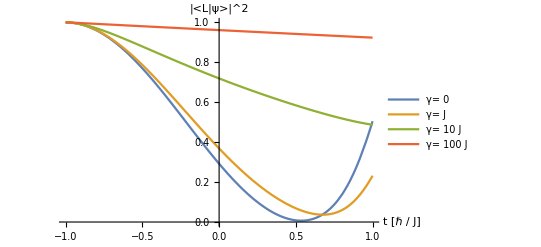

```mathematica
Plot[{ Evaluate[Abs[pL[t^3 / 2,0][t]]^2/. PSoln], Evaluate[Abs[pL[t^3 / 2,1][t]]^2/. PSoln], Evaluate[Abs[pL[t^3 / 2,10][t]]^2/. PSoln], Evaluate[Abs[pL[t^3 / 2,100][t]]^2/. PSoln]},{t,-1,1},PlotLegends->{"γ= 0", "γ= J", "γ= 10 J", "γ= 100 J"}, AxesLabel->{"t [ℏ / J]","|<L|ψ>|^2"}]
```

Also seeing non-Hermitian loss of molecules, however. Need to improve adiabaticity?

```mathematica
Manipulate[Plot[{ Evaluate[pL[a*t^3 +b t^2/ 2 + c t +d,γ][t]*Conjugate[pL[a*t^3 +b t^2/ 2 + c t+d,γ][t]]/. PSoln]},{t,-1,1}, AxesLabel->{"t [ℏ / J]","|<L|ψ>|^2"}, PlotRange->{0,1}],{γ,0,200}, {a,-10,10}, {b,-10,10}, {c,-10,10}, {d,0,10}]
```

Reproducing fig 1 from paper (with roughly selected ramp parameters)

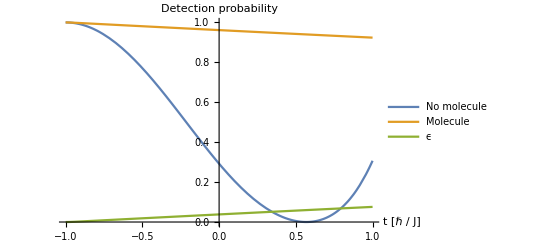

```mathematica
Plot[{ Evaluate[Abs[pL[-0.2t^3 -0.35 t^2 + 0.25 t,0][t]]^2/. PSoln], Evaluate[Abs[pL[-0.2t^3 -0.35 t^2 + 0.25 t,100][t]]^2/. PSoln], Evaluate[1 - Abs[pL[-0.2t^3 -0.35 t^2 + 0.25 t,100][t]]^2 - Abs[pR[-0.2t^3 -0.35 t^2 + 0.25 t,100][t]]^2/. PSoln]},{t,-1,1},PlotLegends->{"No molecule", "Molecule", "ϵ", "γ= 100 J"}, AxesLabel->{"t [ℏ / J]","Detection probability"}]
```

```mathematica
Evaluate[1 - Abs[pL[-0.2t^3 -0.35 t^2 + 0.25 t,500][t]]^2 - Abs[pR[-0.2t^3 -0.35 t^2 + 0.25 t,500][t]]^2/. PSoln /. t-> 0.6]
```

ParametricNDSolve::prange: Invalid non-numeric value 0.25 t-0.35 t^2-0.2 t^3 for parameter Δ.

0.0126712